11 Derivadas
11.1 Cálculo de derivadas

```mathematica
D[3x^2+8x,x]
```

8+6 x

```mathematica
D[4y^5-6y^3,y]
```

-18 y^2+20 y^4

```mathematica
D[Sin[x*y^2],x] (* Derivada respecto a x *)
D[Sin[x*y^2],y] (* Derivada respecto a y *)
```

y^2 Cos[x y^2]

2 x y Cos[x y^2]

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
f[x_]:=3x^2+8x
f'[x]
```

8+6 x

11.2 Derivadas de orden superior

```mathematica
D[Sin[6x],x,x,x,x,x](* Primera forma, quinta derivada *)
D[Sin[6x],x,x,x,x,x] //HoldForm(* Mostrar cuál derivada se efectua *)
```

7776 Cos[6 x]

∂_(x,x,x,x,x) Sin[6 x]

```mathematica
D[Sin[6x],{x,5}](* Segunda forma, quinta derivada *)
D[Sin[6x],{x,5}] //HoldForm(* Asíntota horizontal igual a 1 *)
```

7776 Cos[6 x]

∂_{x,5} Sin[6 x]

```mathematica
D[Sin[4x+6y],{x,2},{y,3}]
D[Sin[4x+6y],{x,2},{y,3}]//HoldForm
```

3456 Cos[4 x+6 y]

∂_({x,2},{y,3}) Sin[4 x+6 y]

11.3 Derivadas simbólicas

```mathematica
Clear[f]
```

```mathematica
D[f[x]*g[x],x]
D[f[x]/g[x],x]
D[f[x]*g[x]*h[x],x]
```

g[x] f'[x]+f[x] g'[x]

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

g[x] h[x] f'[x]+f[x] h[x] g'[x]+f[x] g[x] h'[x]

11.4 Cálculo de tangentes a curvas

```mathematica
f[x_]:=x^2+3x
```

```mathematica
f'[2](* Pendiente de la recta tangente en x=2 *)
f[2] (* Ordenada al origen de la recta tangente en x=2 *)
```

7

10

```mathematica
f[2]+f'[2](x-2)(* Ec. de la recta tangente a f en x=2 *)
```

10+7 (-2+x)

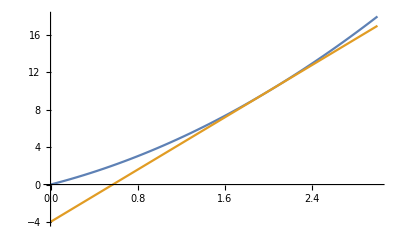

```mathematica
Plot[{f[x],10+7 (-2+x)},{x,0,3}]
```

11.5 Extremos y puntos de inflexión

```mathematica
f[x_]:=x^3-6x+7
```

```mathematica
Solve[f'[x]==0,x] (* Puntos críticos *)
```

{{x→-√2},{x→√2}}

```mathematica
Solve[f''[x]==0,x] (* Puntos críticos - inflexión *)
```

{{x→0}}

```mathematica
f''[√2](* Determina un máximo *)
f''[-√2](* Determina un mínimo *)
```

6 √2

-6 √2

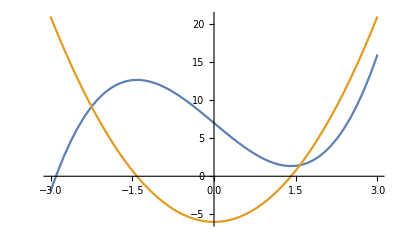

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

11.6 Polinomios de Taylor

```mathematica
Series[Exp[x],{x,0,7}]
Normal[Series[Exp[x],{x,0,7}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+O[x]^8

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040

1-x^4/2+x^8/24-x^12/720+x^16/40320

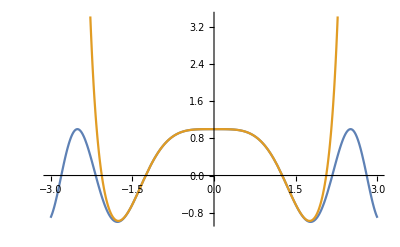

```mathematica
f[x_]=Normal[Series[Cos[x^2],{x,0,16}]]
Plot[{Cos[x^2],f[x]},{x,-3,3}]
```

1-x^4/2+x^8/24-x^12/720+x^16/40320-x^20/3628800+x^24/479001600-x^28/87178291200

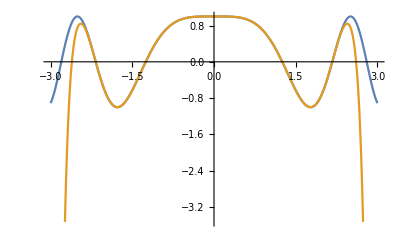

```mathematica
f[x_]=Normal[Series[Cos[x^2],{x,0,28}]]
Plot[{Cos[x^2],f[x]},{x,-3,3}] (* Mejor aproximación *)
```